FE analysis of plate bending using Bogner-Fox-Schmit shape functions, which guarantee C^1 interelement continuity.
(c) 2019 Yury Vetyukov, TU Wien, Austria
See
- Yu. Vetyukov, Finite element modeling of Kirchhoff-Love shells as smooth material surfaces, ZAMM-Journal of Applied Mathematics and Mechanics/Zeitschrift für Angewandte Mathematik und Mechanik, Vol. 94, Issue 1-2, 2014, pp. 150-163
- Yu. Vetyukov, Nonlinear mechanics of thin-walled structures: asymptotics, direct approach and numerical analysis, Springer, 2014
for details and convergence studies.

### shape functions, degrees of freedom and approximation

the element has four nodes and features cubic shape functions, such that the deflection itself, the two first order derivatives and the mixed second order derivative of the deflection with respect to the local coordinates q1, q2  appear as nodal degrees of freedom

shape functions for the approximation of the lateral deflection

```mathematica
sfGeneral=(q2-1)^2 (q1-1)^2{(2+q2)  (2+q1),k1 (2+q2)  (1+q1),k2 (1+q2)  (2+q1),k1 k2(1+q2)  (1+q1)}/16/.{q1->k1 q1,q2->k2 q2};
Table[Plot3D[sf,{q1,-1,1},{q2,-1,1},ImageSize->160],{sf,sfGeneral/.{k1->1,k2->1}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
sf=sfGeneral/.{{k1->1,k2->1},{k1->-1,k2->1},{k1->-1,k2->-1},{k1->1,k2->-1}};
sf//TableForm
```

1/16 (-1+q1)^2 (2+q1) (-1+q2)^2 (2+q2) | 1/16 (-1+q1)^2 (1+q1) (-1+q2)^2 (2+q2) | 1/16 (-1+q1)^2 (2+q1) (-1+q2)^2 (1+q2) | 1/16 (-1+q1)^2 (1+q1) (-1+q2)^2 (1+q2)
1/16 (-1-q1)^2 (2-q1) (-1+q2)^2 (2+q2) | -1/16 (-1-q1)^2 (1-q1) (-1+q2)^2 (2+q2) | 1/16 (-1-q1)^2 (2-q1) (-1+q2)^2 (1+q2) | -1/16 (-1-q1)^2 (1-q1) (-1+q2)^2 (1+q2)
1/16 (-1-q1)^2 (2-q1) (-1-q2)^2 (2-q2) | -1/16 (-1-q1)^2 (1-q1) (-1-q2)^2 (2-q2) | -1/16 (-1-q1)^2 (2-q1) (-1-q2)^2 (1-q2) | 1/16 (-1-q1)^2 (1-q1) (-1-q2)^2 (1-q2)
1/16 (-1+q1)^2 (2+q1) (-1-q2)^2 (2-q2) | 1/16 (-1+q1)^2 (1+q1) (-1-q2)^2 (2-q2) | -1/16 (-1+q1)^2 (2+q1) (-1-q2)^2 (1-q2) | -1/16 (-1+q1)^2 (1+q1) (-1-q2)^2 (1-q2)

degrees of freedom in a local node number i

```mathematica
dofLocal[n_]:={Subscript[W, n],Subscript[W1, n],Subscript[W2, n],Subscript[W12, n]}
```

approximation for the deflection on a finite element

```mathematica
w=Sum[sf[[n,m]]dofLocal[n][[m]],{n,4},{m,4}];
```

and we plot four elements with a sample deformation - one of the d.o.f. in the middle node is varied, and the surface remains smooth

```mathematica
Table[
Show[
Plot3D[
w/.{Subscript[W, 1]->1,Subscript[W1, 1]->a,Subscript[W2, 1]->0,Subscript[W12, 1]->0,Subscript[W, 2]->1,Subscript[W1, 2]->0,Subscript[W2, 2]->1,Subscript[W12, 2]->0,Subscript[W, 3]->0,Subscript[W1, 3]->0,Subscript[W2, 3]->0,Subscript[W12, 3]->0,Subscript[W, 4]->0,Subscript[W1, 4]->0,Subscript[W2, 4]->0,Subscript[W12, 4]->0}/.{q1->x-1,q2->y-1},
{x,0,2},{y,0,2},
PlotStyle->Red,PlotRange->All
],
Plot3D[
w/.{Subscript[W, 1]->0,Subscript[W1, 1]->0,Subscript[W2, 1]->0,Subscript[W12, 1]->0,Subscript[W, 2]->1,Subscript[W1, 2]->a,Subscript[W2, 2]->0,Subscript[W12, 2]->0,Subscript[W, 3]->0,Subscript[W1, 3]->0,Subscript[W2, 3]->0,Subscript[W12, 3]->0,Subscript[W, 4]->0,Subscript[W1, 4]->0,Subscript[W2, 4]->0,Subscript[W12, 4]->0}/.{q1->x+1,q2->y-1},
{x,-2,0},{y,0,2},
PlotStyle->Green,PlotRange->All
],
Plot3D[
w/.{Subscript[W, 1]->0,Subscript[W1, 1]->0,Subscript[W2, 1]->0,Subscript[W12, 1]->0,Subscript[W, 2]->0,Subscript[W1, 2]->0,Subscript[W2, 2]->0,Subscript[W12, 2]->0,Subscript[W, 3]->1,Subscript[W1, 3]->a,Subscript[W2, 3]->0,Subscript[W12, 3]->0,Subscript[W, 4]->0,Subscript[W1, 4]->0,Subscript[W2, 4]->0,Subscript[W12, 4]->0}/.{q1->x+1,q2->y+1},
{x,-2,0},{y,-2,0},
PlotStyle->Blue,PlotRange->All
],
Plot3D[
w/.{Subscript[W, 1]->0,Subscript[W1, 1]->0,Subscript[W2, 1]->0,Subscript[W12, 1]->0,Subscript[W, 2]->0,Subscript[W1, 2]->0,Subscript[W2, 2]->0,Subscript[W12, 2]->0,Subscript[W, 3]->1,Subscript[W1, 3]->0,Subscript[W2, 3]->1,Subscript[W12, 3]->0,Subscript[W, 4]->1,Subscript[W1, 4]->a,Subscript[W2, 4]->0,Subscript[W12, 4]->0}/.{q1->x-1,q2->y+1},
{x,0,2},{y,-2,0},
PlotStyle->Yellow,PlotRange->All
],
PlotRange->All
],
{a,-1,1}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

### plate: potential energy and strain energy

the size of the finite element is h, and dx = h/2 dq1, dy = h/2 dq2, and during integration dx dy = h^2/4 dq1 dq2.
now we can integrate the potential of external forces - energy in the field of gravity; g is the gravity acceleration, and ρ is the density per unit area

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GP=GaussianQuadratureWeights[4,-1,1];
IntegrateElement[f_]:=Sum[H^2/4gp1[[2]]gp2[[2]]f/.{q1->gp1[[1]],q2->gp2[[1]]},{gp1,GP},{gp2,GP}]
```

potential energy in the field of gravity

```mathematica
UelExt=Expand[IntegrateElement[ρ h g w]];
```

curvature and strain energy

```mathematica
κ=4/H^2 D[w,{{q1,q2},2}];
UelDef=Expand[1/2 IntegrateElement[D1 Tr[κ]^2+D2 Tr[κ.κ]]];
LeafCount[UelDef]
```

3233

values are correct on a rigid body translation

```mathematica
Chop[{UelExt,UelDef}/.Flatten[Table[Thread[dofLocal[i]->{1,0,0,0}],{i,4}]]]
```

{0.0625 a^2 g h ρ,0}

### now we assemble the system; the square plate has dimensions a×a and is divided into n×n elements, the parameters are also specified

```mathematica
n=4;
H:=a/n;
```

```mathematica
params={a->1,g->9.8,D1->(Ε ν h)/(1-ν^2)h^2/12,D2->(Ε h)/(1+ν)h^2/12,ρ->7800,Ε->2.1 10^11,ν->0.3,h->10^-3};
```

this function below replaces local variables on a f.e. by global variables, which are double-indexed

```mathematica
LocalToGlobal[i_,j_]:={Subscript[e_, 1]->Subscript[e, i-1,j-1],Subscript[e_, 2]->Subscript[e, i,j-1],Subscript[e_, 3]->Subscript[e, i,j],Subscript[e_, 4]->Subscript[e, i-1,j]}
```

```mathematica
{Uext,Udef}=Sum[{UelExt,UelDef}/.LocalToGlobal[i,j],{i,n},{j,n}]//.params;
```

all degrees of freedom

```mathematica
dofAll=Flatten[Table[dofLocal[i]/.Subscript[u_, i]->Subscript[u, p,q],{p,0,n},{q,0,n}]];
Length[dofAll]
```

100

and now the boundary conditions: the plate is clamped at all four edges, and all degrees of freedom at these edges are to be constrained

```mathematica
dofConstrained=Flatten[{
Table[dofLocal[1]/.LocalToGlobal[1,j],{j,n}],
Table[dofLocal[3]/.LocalToGlobal[n,j],{j,n}],
Table[dofLocal[2]/.LocalToGlobal[i,1],{i,n}],
Table[dofLocal[4]/.LocalToGlobal[i,n],{i,n}]
}];
constraints=Thread[dofConstrained->0];
```

```mathematica
constraints;
```

we exclude the constrained d.o.f. and remain just with the active ones

```mathematica
dofActive=DeleteCases[dofAll,z_/;MemberQ[dofConstrained,z]];
Length[dofActive]
```

36

in the linear problem we can simply neglect the constrained dof when computing the stiffness matrix and the column of the right hand side

```mathematica
K=2CoefficientArrays[Udef,dofActive,"Symmetric"->True][[3]];
F=-CoefficientArrays[Uext,dofActive][[2]];
```

```mathematica
MatrixForm[K];
```

```mathematica
MatrixForm[F];
```

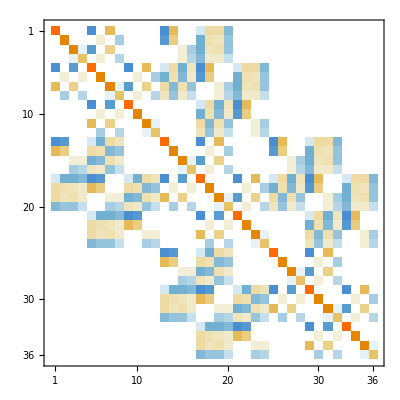

```mathematica
MatrixPlot[K]
```

### results of static analysis

deformed shape with a scaling factor

```mathematica
plotSol[factor_,sol_]:=Show[
ParallelTable[
ParametricPlot3D[
{
(i-1+(q1+1)/2)H,
(j-1+(q2+1)/2)H,
factor w/.LocalToGlobal[i,j]/.constraints/.Thread[dofActive->sol]
}/.params,
{q1,-1,1},{q2,-1,1},
MaxRecursion->0,PlotPoints->{2,2}
],
{i,n},{j,n}
],
PlotRange->All
]
```

```mathematica
staticSol=LinearSolve[K,F]
```

{-0.00183177,-0.00108061,-0.00108061,-0.000662254,-0.00301402,-0.00182128,-1.94278×10^-19,6.31189×10^-21,-0.00183177,-0.00108061,0.00108061,0.000662254,-0.00301402,3.59823×10^-20,-0.00182128,-2.20182×10^-19,-0.0050277,-2.8837×10^-19,-5.63273×10^-19,1.66838×10^-19,-0.00301402,-4.7153×10^-20,0.00182128,4.25825×10^-19,-0.00183177,0.00108061,-0.00108061,0.000662254,-0.00301402,0.00182128,-2.40918×10^-19,5.61217×10^-19,-0.00183177,0.00108061,0.00108061,-0.000662254}

deflection in the center and its exact value

```mathematica
Subscript[W, n/2,n/2]/.Thread[dofActive->staticSol]
-1.265319087 10^-3(ρ g h a^4)/(D1+D2)//.params
```

-0.0050277

-0.00502949

```mathematica
plotSol[-50,staticSol]
```

-Graphics3D-

### concentrated force in the middle

```mathematica
posCentralNode=Position[dofActive,Subscript[W, n/2,n/2]]⟦1,1⟧
```

17

the force is the same as the own weight

```mathematica
Fconcentrated=Table[If[i==posCentralNode,ρ g h a^2/.params,0],{i,Length[dofActive]}];
solConcentrated=LinearSolve[K,Fconcentrated];
maxDisplConcentrated=Max[solConcentrated]
```

0.0217995

deflection under distributed weight - for comparison

```mathematica
Subscript[W, n/2,n/2]/.Thread[dofActive->staticSol]
```

-0.0050277

```mathematica
plotSol[20,solConcentrated]
```

-Graphics3D-

### eigenfrequency analysis

kinetic energy of an element as if deflections were velocities

```mathematica
Tel=1/2 IntegrateElement[ρ h w^2];
```

of the entire plate

```mathematica
T=Sum[Tel/.LocalToGlobal[i,j],{i,n},{j,n}]//.params;
```

mass matrix

```mathematica
M=2CoefficientArrays[T,dofActive,"Symmetric"->True][[3]];
```

eigenvalue problem

```mathematica
Reverse[Sqrt[Eigenvalues[{K,M},-15]]/(2*Pi)]
```

{9.01081,18.501,18.501,27.3611,33.6236,33.7485,42.2358,42.2358,56.8246,60.9078,60.9078,68.5815,68.7213,82.2147,82.2147}

```mathematica
eigenmodes=Reverse[Eigensystem[{K,M},-1][[2]]];
Table[Show[plotSol[1,em],ImageSize->250,Boxed->False,Axes->False],{em,eigenmodes}];
```